```mathematica
SetOptions[{Fourier,InverseFourier,FourierMatrix},FourierParameters->{1,1}];
```

```mathematica
$ModulesTargetPath="C:\\Users\\Christian Volmer\\Documents\\Projekte\\offt\\offt\\src\\backend\\standard_modules";
$ModuleSizes={};
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"FftDefinitionsReIm.wl"}]];
```

## Programs

### Basics

```mathematica
Unprotect[Program,InVar,OutVar,TempVar];
ClearAll[Program,InVar,OutVar,TempVar];
Program::usage="";InVar::usage="";OutVar::usage="";TempVar::usage="";
Protect[Program,InVar,OutVar,TempVar];
```

### ProgramForLength

```mathematica
ProgramForLength[length_]:=Module[{
transformationList,
graph,
matrix,
variables
},

transformationList=List@@FftReal[length];
graph=ArrayFlatten[DiagonalMatrix[Reverse@Array[matrix,Length[transformationList]]]/.{matrix[i_]:>transformationList⟦i⟧}];
graph=Join[ConstantArray[0,{2length,Dimensions[graph]⟦2⟧}],graph];
graph=Join[graphᵀ,ConstantArray[0,{2length,Dimensions[graph]⟦1⟧}]]ᵀ;

variables=Join[
Array[InVar,2length],
Array[TempVar,Length[graph]-4length],
Array[OutVar,2length]
];

Program[<|"Length"->length,"Graph"->graph,"Variables"->variables|>]
]
```

### ProgramRun

```mathematica
ClearAll[ProgramRun];
ProgramRun[program_Program,input_List]:=Module[{
length=program⟦1,"Length"⟧,
graph=program⟦1,"Graph"⟧,
variables=program⟦1,"Variables"⟧,
memory,
inputReIm,line,
result
},

If[Length[input]=!=length,Return[$Failed]];

memory=variables;
inputReIm=Flatten[ReIm[input]];
memory=Replace[memory,{InVar[i_]:>inputReIm⟦i⟧,_->0},{1}];

Do[
memory⟦i⟧=memory.graph⟦i⟧;
,
{i,2length+1,Length[graph]}
];

result=Array[OutVar,2length]/.Thread[variables->memory];
Complex@@@Partition[result,2]
]
```

### ProgramCheckFft

```mathematica
ClearAll[ProgramCheckFft];
ProgramCheckFft[program_Program]:=
(Union[Chop[ProgramRun[program,#]-Fourier[#],1*^-6]]==={0})&[RandomComplex[{-1-I,1+I},program⟦1⟧⟦"Length"⟧]];
```

### ProgramPlot

```mathematica
ClearAll[ProgramPlot];
ProgramPlot[program_Program]:=Module[{graph=program⟦1⟧⟦"Graph"⟧,x},
MatrixPlot[graph+x IdentityMatrix[Length[graph]],MaxPlotPoints->Infinity,Mesh->All,ColorRules->{0->White,1->Black,-1->Green,x->Gray,_?(!FreeQ[#,x]&)->Yellow,_->Red},ImageSize->800,FrameTicks->({#,#,#,#}&[Range[5,Length[graph],5]])]]
```

### ProgramMoveRight

```mathematica
ClearAll[ProgramMoveRight];
ProgramMoveRight[program_Program]:=Module[{
length=program⟦1,"Length"⟧,
graph=program⟦1,"Graph"⟧,
variables=program⟦1,"Variables"⟧,
start,stop,
perm,before,current,
lastFirst
},

lastFirst=#⟦{-1,1}⟧&;

start=2length+1;
stop=Length[graph];

current=graph;
While[
before=current;
perm=start-1+OrderingBy[Sign[Abs[current⟦start;;stop⟧]],lastFirst[Flatten[Position[#,1,{1},Heads->False]]]&];
perm=Join[Range[start-1],perm,Range[stop+1,Length[graph]]];
current=current⟦perm,perm⟧;
variables=variables⟦perm⟧;
current=!=before
];
Program[<|"Length"->length,"Graph"->current,"Variables"->variables|>]
];
```

```mathematica
ProgramDeleteIdentities[program_Program]:=Module[{
length=program⟦1,"Length"⟧,
graph=program⟦1,"Graph"⟧,
variables=program⟦1,"Variables"⟧,
i,p
},

i=2length+1;
While[i<=Length[graph],
p=Flatten[Position[graph⟦i⟧,Except[0],{1},Heads->False]];
If[Length[p]===1&&(p=p⟦1⟧;graph⟦i⟧⟦p⟧===1),
graph⟦All,p⟧+=graph⟦All,i⟧;
If[MatchQ[variables⟦i⟧,_OutVar],
variables⟦p⟧=variables⟦i⟧
];
p=Complement[Range[Length[graph]],{i}];
variables=variables⟦p⟧;
graph=graph⟦p,p⟧;
,
(* else *)
++i
]
];
Program[<|"Length"->length,"Graph"->graph,"Variables"->variables|>]
];
```

```mathematica
ProgramDeleteIdentities2[program_Program]:=Module[{
length=program⟦1,"Length"⟧,
graph=program⟦1,"Graph"⟧,
variables=program⟦1,"Variables"⟧,
lines,
i,p
},

i=2length+1;
lines=Range[Length[graph]];
While[i<=Length[lines],
p=Flatten[Position[graph⟦lines⟦i⟧,lines⟧,Except[0],{1},Heads->False]];
If[Length[p]===1&&(p=p⟦1⟧;graph⟦lines⟦i⟧,lines⟦p⟧⟧===1),
graph⟦lines,lines⟦p⟧⟧+=graph⟦lines,lines⟦i⟧⟧;
If[MatchQ[variables⟦lines⟦i⟧⟧,_OutVar],
variables⟦lines⟦p⟧⟧=variables⟦lines⟦i⟧⟧
];
lines=Complement[lines,{lines⟦i⟧}];
,
(* else *)
++i
]
];
Program[<|"Length"->length,"Graph"->graph⟦lines,lines⟧,"Variables"->variables⟦lines⟧|>]
]
```

```mathematica
orig=ProgramForLength[7];
AbsoluteTiming[prog=ProgramDeleteIdentities[orig];]
AbsoluteTiming[prog2=ProgramDeleteIdentities2[orig];]

prog=ProgramMoveRight[prog];
prog2=ProgramMoveRight[prog2];

prog===prog2
ProgramCheckFft[prog]
```

{0.0163348,Null}

{0.0086435,Null}

True

True

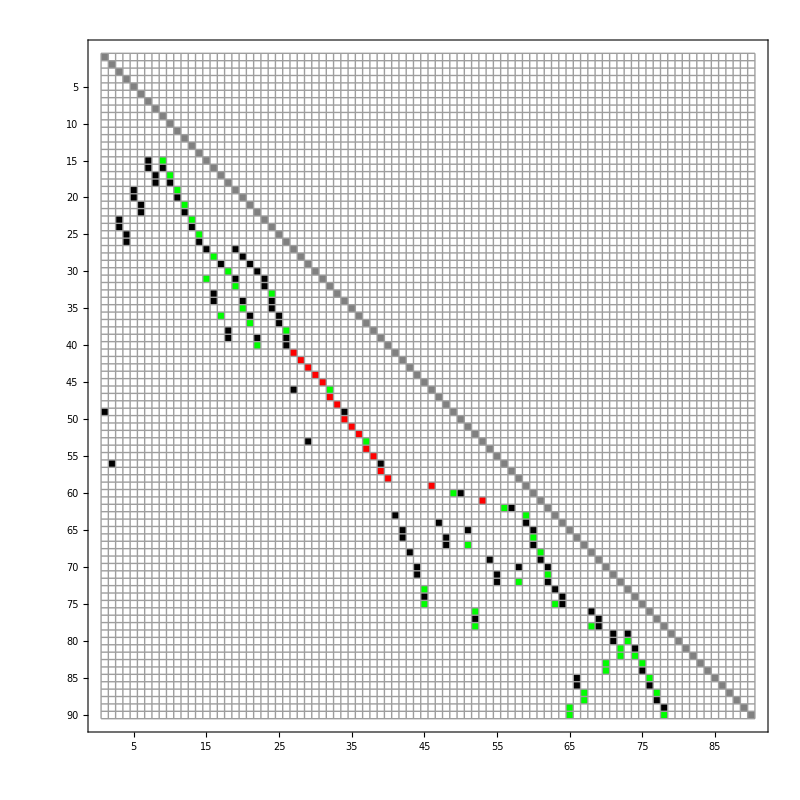

{InVar[1],InVar[2],InVar[3],InVar[4],InVar[5],InVar[6],InVar[7],InVar[8],InVar[9],InVar[10],InVar[11],InVar[12],InVar[13],InVar[14],TempVar[7],TempVar[9],TempVar[8],TempVar[10],TempVar[5],TempVar[11],TempVar[6],TempVar[12],TempVar[3],TempVar[13],TempVar[4],TempVar[14],TempVar[21],TempVar[25],TempVar[22],TempVar[26],TempVar[19],TempVar[17],TempVar[29],TempVar[23],TempVar[27],TempVar[20],TempVar[18],TempVar[30],TempVar[24],TempVar[28],TempVar[55],TempVar[59],TempVar[56],TempVar[60],TempVar[53],TempVar[47],TempVar[51],TempVar[63],OutVar[1],TempVar[57],TempVar[61],TempVar[54],TempVar[48],TempVar[52],TempVar[64],OutVar[2],TempVar[58],TempVar[62],TempVar[65],TempVar[75],TempVar[66],TempVar[76],TempVar[73],TempVar[69],TempVar[93],TempVar[95],TempVar[91],TempVar[74],TempVar[70],TempVar[94],TempVar[96],TempVar[92],TempVar[89],TempVar[87],TempVar[85],TempVar[90],TempVar[88],TempVar[86],OutVar[8],OutVar[10],OutVar[4],OutVar[14],OutVar[6],OutVar[12],OutVar[7],OutVar[9],OutVar[3],OutVar[13],OutVar[5],OutVar[11]}

```mathematica
ProgramPlot[prog]
prog⟦1,"Variables"⟧
```

## Template

```mathematica
template="
//          Copyright Christian Volmer 2022, 2023.
// Distributed under the Boost Software License, Version 1.0.
//    (See accompanying file LICENSE_1_0.txt or copy at
//          https://www.boost.org/LICENSE_1_0.txt)

#include \"../standard_module.h\"

namespace offt {
namespace backend {

/*
\tNumber of additions       : <additionCount>
\tNumber of multiplications : <multiplicationCount>
*/

template<> StandardModuleComplexity const StandardModule<float, <length>>::Complexity = { <additionCount>, <multiplicationCount> };
template<> StandardModuleComplexity const StandardModule<double, <length>>::Complexity = { <additionCount>, <multiplicationCount> };

template<typename valueT>
static void ComputeCore(Phasors<valueT> const &phasors, valueT *pReal, valueT *pImag, ptrdiff_t stride, size_t twiddleStart, size_t twiddleIncrement)
{
\t<temps>

\t<twiddle>

\t<computations>
}

template<> void StandardModule<float, <length>>::Compute(float *pReal, float *pImag, ptrdiff_t stride, size_t twiddleStart, size_t twiddleIncrement) const
{
\tComputeCore(mPhasors, pReal, pImag, stride, twiddleStart, twiddleIncrement);
}

template<> void StandardModule<double, <length>>::Compute(double *pReal, double *pImag, ptrdiff_t stride, size_t twiddleStart, size_t twiddleIncrement) const
{
\tComputeCore(mPhasors, pReal, pImag, stride, twiddleStart, twiddleIncrement);
}

}
}
";
```

## Transformation List

```mathematica
ClearAll[IdentityMatrixQ];
IdentityMatrixQ[m_]:=TrueQ[MatrixQ[m]&&Equal@@Dimensions[m]&&IdentityMatrix[Length[m]]==m];
```

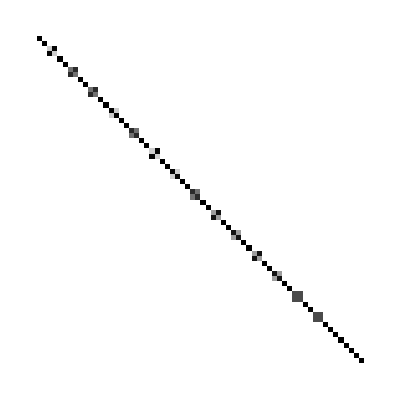
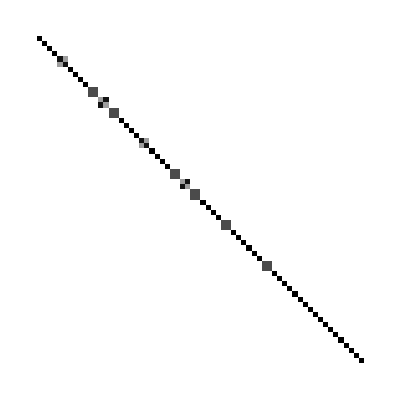
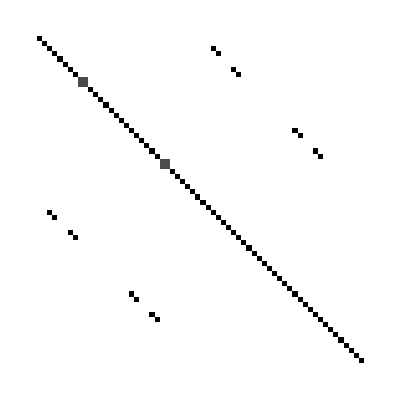
TransformationList[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-]

```mathematica
ArrayPlot/@transformationListForFftSize[32]
```

## General Code Generation

```mathematica
numberToString[n_]:=Which[
IntegerQ[n]&&n<0,"-"<>IntegerString[n],
IntegerQ[n]&&n>=0,IntegerString[n],
True,"valueT("<>ToString[CForm[N[n,20]]]<>")"];

rhsString[varsIn_,coeffsIn_]:=Module[{
nonz,vars,coeffs,t,mults,ops},

nonz=Flatten[Position[coeffsIn,_?(#!=0&),{1},Heads->False]];
vars=varsIn⟦nonz⟧;
coeffs=coeffsIn⟦nonz⟧;

If[Length[vars]>1&&Equal@@Abs[coeffs]&&Abs[coeffs⟦1⟧]!=1,
numberToString[Abs[coeffs⟦1⟧]]<>" * ("<>rhsString[vars,coeffs/Abs[coeffs⟦1⟧]]<>")"
,
(* else *)
mults=Which[
#==1,"",
#==-1,"",
True,numberToString[Abs[#]]<>" * "
]&/@coeffs;

ops=If[#<0," - "," + "]&/@coeffs;
ops⟦1⟧=If[First[coeffs]<0,"-",""];

StringJoin[Transpose[{ops, mults,vars}]]
]
];

assignmentString[lhs_,rhs_,coeffs_]:=Module[
{lhsPosition,rhs2,coeffs2,ordering},

lhsPosition=Position[rhs,lhs,{1},Heads->False];
If[Length[lhsPosition]>=1,
lhsPosition=lhsPosition⟦1,1⟧;
rhs2=Delete[rhs,lhsPosition];
coeffs2=Delete[coeffs,lhsPosition];
,
lhsPosition=0;
];

Which[
Length[rhs]===1&&lhsPosition===1,
lhs<>" *= "<>numberToString[coeffs⟦1⟧]<>";",

lhsPosition>0&&coeffs⟦lhsPosition⟧==1&&First[coeffs2]>=0,
lhs<>" += "<>rhsString[rhs2,coeffs2]<>";",

lhsPosition>0&&coeffs⟦lhsPosition⟧==1&&First[coeffs2]<0,
lhs<>" -= "<>rhsString[rhs2,-coeffs2]<>";",

True,
ordering=Ordering[-Sign[coeffs]];
rhs2=rhs⟦ordering⟧;
coeffs2=coeffs⟦ordering⟧;
lhs<>" = "<>rhsString[rhs2,coeffs2]<>";"
]
]
```

## Playground

```mathematica
ExecuteOperations[operations_,input_]:=Module[{
variables,i},

variables=PadRight[input,Length[operations]];
Do[variables⟦i⟧=operations⟦i⟧.variables,{i,Length[input]+1,Length[operations]}];
Take[variables,-Length[input]]
];
```

```mathematica
CheckOperations[operations_,length_]:=Module[{
input,result
},
input=RandomReal[{-1,1},2length];
result=ExecuteOperations[operations,input];
Union[Chop[result-ArrayFlatten[Map[ComplexMultiplicationMatrix,N@FourierMatrix[length],{2}]].input]]==={0}
];
```

```mathematica
RemoveIdentityOperations[operations_,length_]:=Module[{
op=operations
},

Module[{
i,p
},
i=1;
While[i<Length[op]-2length,
p=Flatten[Position[op⟦i⟧,Except[0],{1},Heads->False]];
If[Length[p]===1&&(p=p⟦1⟧;op⟦i⟧⟦p⟧===1),
op⟦All,p⟧+=op⟦All,i⟧;
p=Complement[Range[Length[op]],{i}];
op=op⟦p,p⟧;
,
(* else *)
++i
]
]
];
op
]
```

```mathematica
(* Scheint kaputt zu sein, Fehler bei 25 *)
MoveUpOperations[operations_,length_]:=Module[{
op2,
i=2length+1,
stop=Length[operations]-2length,
map,
a,ancestors,
n,neighbours
},

op2=operations;
map=Sign[Abs[op2]];

While[i<=stop,

ancestors=Flatten[Position[map⟦i⟧,1]];
neighbours=Union[Flatten[Table[Position[map⟦All,a⟧,1,{1},Heads->False],{a,ancestors}]]];
++i;
neighbours=Complement[neighbours,Range[i],Range[stop+1,Length[op2]]];
Do[
op2=MoveFromTo[op2,n,i];
map=MoveFromTo[map,n,i];
++i;
,
{n,neighbours}
];
];
op2
];
```

```mathematica
lastFirst[x_]:={Last[x],First[x]};
```

```mathematica
MoveRightOperations[operations_,length_]:=Module[{
start=2length+1,
stop=Length[operations]-2length,
perm,before,current
},

current=operations;
While[
before=current;
perm=start-1+OrderingBy[Sign[Abs[current⟦start;;stop⟧]],lastFirst[Flatten[Position[#,1,{1},Heads->False]]]&];
perm=Join[Range[start-1],perm,Range[stop+1,Length[operations]]];
current=current⟦perm,perm⟧;
current=!=before
];
current
];
```

```mathematica
OperationsPlot[op_,length_]:=MatrixPlot[op,MaxPlotPoints->Infinity,Mesh->All,FrameTicks->({#,#,#,#}&@Range[1,Length[operations],2]),ColorRules->{0->White,1->Black,-1->Green,_->Red},ImageSize->800]
```

```mathematica
MoveFromTo[operations_,from_,to_]:=Module[{
perm
},

perm=Delete[Range[Length[operations]],from];
perm=Insert[perm,from,to];
operations⟦perm,perm⟧
];
```

```mathematica
ClearAll[TraverseAndSowOld];
TraverseAndSowOld[operations_,i_]:=Module[{
src
},

src=Flatten[Position[operations⟦i⟧,Except[0],{1},Heads->False]];
TraverseAndSow[operations,#]&/@src;
Sow[i];
];
```

```mathematica
ClearAll[TraverseAndSow];
TraverseAndSow[operations_,node_]:=Module[{
visited,
visit
},

visited[_]=False;
visit[n_]:=If[!visited[n],
visited[n]=True;
Sow[n];
visit/@Flatten[Position[operations⟦n⟧,Except[0],{1},Heads->False]];
];

If[ArrayQ[node],
visit/@node,
visit[node]
];
]
```

```mathematica
length=4;
operations=transformationListForFftSize[length];
operations=ArrayFlatten[DiagonalMatrix[Reverse@Array[x,Length[operations]]]/.{x[i_]:>operations⟦i⟧}];
operations=Join[ConstantArray[0,{2length,Length[operations]}],operations];
operations=Join[operationsᵀ,ConstantArray[0,{2length,Dimensions[operations]⟦1⟧}]]ᵀ;
Dimensions[operations]
AbsoluteTiming[operations=RemoveIdentityOperations[operations,length];]
Dimensions[operations]
CheckOperations[operations,length]
OperationsPlot[operations,length]
```

ArrayFlatten::depth: The ArrayDepth of the expression at position 1 of … must be at least equal to the specified rank 2. (The rank is given by the optional second argument, which defaults to 2.)

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of x⟦{3,43,5,47,4,11,13,38,37,17,«40»},{3,43,5,47,4,11,13,38,37,17,«40»}⟧.

Join::heads: Heads List and TransformationListSimplify at positions 1 and 2 are expected to be the same.

Join::heads: Heads Transpose and List at positions 1 and 2 are expected to be the same.

{1}

{0.0000468,Null}

{1}

Take::take: Cannot take positions -8 through -1 in {0.321315}.

False

MatrixPlot::mat0: Argument Transpose[Join[Transpose[Join[{{0},{0},{0},{0},{0},{0},{0},{0}},TransformationListSimplify[ArrayFlatten[TransformationList[{«4»},{«4»},{«4»},{«4»}]]]]],{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}]] at position 1 is not a matrix.

MatrixPlot[Transpose[Join[Transpose[Join[{{0},{0},{0},{0},{0},{0},{0},{0}},TransformationListSimplify[ArrayFlatten[TransformationList[{{{{0,0,0,1},{0,0,0,0}},{{0,0,0,0},{0,0,0,1}}},{{{0,1,0,0},{0,0,0,0}},{{0,0,0,0},{0,1,0,0}}},{{{0,0,1,0},{0,0,0,0}},{{0,0,0,0},{0,0,1,0}}},{{{1,0,0,0},{0,0,0,0}},{{0,0,0,0},{1,0,0,0}}}},{{{{1,0,-1,0},{0,0,0,0}},{{0,0,0,0},{1,0,-1,0}}},{{{1,0,1,0},{0,0,0,0}},{{0,0,0,0},{1,0,1,0}}},{{{0,1,0,-1},{0,0,0,0}},{{0,0,0,0},{0,1,0,-1}}},{{{0,1,0,1},{0,0,0,0}},{{0,0,0,0},{0,1,0,1}}}},{{{{1,0,0,0},{0,0,0,0}},{{0,0,0,0},{1,0,0,0}}},{{{0,1,0,0},{0,0,0,0}},{{0,0,0,0},{0,1,0,0}}},{{{0,0,0,0},{0,0,-1,0}},{{0,0,1,0},{0,0,0,0}}},{{{0,0,0,1},{0,0,0,0}},{{0,0,0,0},{0,0,0,1}}}},{{{{1,0,-1,0},{0,0,0,0}},{{0,0,0,0},{1,0,-1,0}}},{{{1,0,1,0},{0,0,0,0}},{{0,0,0,0},{1,0,1,0}}},{{{0,1,0,-1},{0,0,0,0}},{{0,0,0,0},{0,1,0,-1}}},{{{0,1,0,1},{0,0,0,0}},{{0,0,0,0},{0,1,0,1}}}}]]]]],{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}]],MaxPlotPoints→∞,Mesh→All,FrameTicks→{{1},{1},{1},{1}},ColorRules→{0→GrayLevel[1],1→GrayLevel[0],-1→RGBColor[0, 1, 0],_→RGBColor[1, 0, 0]},ImageSize→800]

## Move right

```mathematica
ClearAll[CollectAndSow]
CollectAndSowCore[operations_,i_,depth_]:=Module[{
pos
},

Sow[i];

If[depth>0,
pos=Flatten[Position[Sign[Abs[operations⟦All,i⟧]],1]];
CollectAndSow[operations,#,depth-1]&/@pos;
];
];

CollectAndSow[operations_,i_,depth_]:=If[ArrayQ[i],CollectAndSowCore[operations,#,depth]&/@i,CollectAndSowCore[operations,i,depth]];
```

```mathematica
ClearAll[CollectAndSow];
CollectAndSow[operations_,node_,depth_]:=Module[{
visited,
visit
},

visited[_,_]=False;
visit[n_,d_]:=If[!visited[n,d],
visited[n,d]=True;
Sow[n];
If[d>0,
visit[#,d-1]&/@Flatten[Position[Sign[Abs[operations⟦All,n⟧]],1]];
];
];

If[ArrayQ[node],
visit[#,depth]&/@node,
visit[node,depth]
];
];
```

```mathematica
TestOptimiseOperations[operations_,length_]:=Module[{
op2=operations,
xx,i,depth,perm,
usedVariables,dependants,
inputs,outputs,
stop
},

inputs=Range[2length];
outputs=Length[op2]-2length+inputs;

xx=0;
i=2length+1;
stop=Length[op2]-2length;
While[
i<=stop,

perm={i};
depth=2;
perm=Union[Reap[CollectAndSow[op2,perm,depth]]⟦2,1⟧];
perm=Union[Reap[TraverseAndSow[op2,perm]]⟦2,1⟧];

usedVariables=Flatten[Position[Sign[Total[Sign[Abs[op2⟦perm⟧]]]],1,{1},Heads->False]];
dependants=Union[Reap[CollectAndSow[op2,usedVariables,1]]⟦2,1⟧];

perm=Union[perm,dependants];
perm=Union[Reap[TraverseAndSow[op2,perm]]⟦2,1⟧];

perm=Complement[perm,inputs,outputs];
perm=Join[inputs,perm];
inputs=Range[Length[perm]];
If[Length[perm]=!=xx,
xx=Length[perm];
Print[xx];
If[xx>=Length[op2]-2length,Break[]];
];
perm=Join[perm,Complement[Range[2length+1,Length[op2]],perm]];
op2=op2⟦perm,perm⟧;
++i;
];
op2
];

op2=operations;
AbsoluteTiming[op3=TestOptimiseOperations[MoveRightOperations[op2,length],length];]
CheckOperations[op2,length]
CheckOperations[op3,length]
OperationsPlot[op3,length]
```

```mathematica
opref=op3;
```

```mathematica
opref===op3
```

## Code generation 2

```mathematica
ClearAll[GenerateCppCode];
GenerateCppCode[length_]:=Module[{
operations,x,vars,i,temps,twiddle,computations,additionCount,multiplicationCount
},

Print["Generating size ",length];
operations=transformationListForFftSize[length];
operations=ArrayFlatten[DiagonalMatrix[Reverse@Array[x,Length[operations]]]/.{x[i_]:>operations⟦i⟧}];
operations=Join[ConstantArray[0,{2length,Length[operations]}],operations];
operations=Join[operationsᵀ,ConstantArray[0,{2length,Dimensions[operations]⟦1⟧}]]ᵀ;
operations=RemoveIdentityOperations[operations,length];
operations=MoveRightOperations[operations,length];
operations=TestOptimiseOperations[operations,length];
Print["OK? ",CheckOperations[operations,length]];

vars=StringJoin["t"<>IntegerString[#]]&/@Range[Length[operations]-2length];
vars=Join[
vars,
If[EvenQ[#],"pReal[","pImag["]<>ToString[Floor[#/2]]<>" * stride]"&/@(Range[2length]-1)
];

computations=Table[assignmentString[vars⟦i⟧,vars,operations⟦i⟧],{i,2length+1,Length[operations]}];

temps=Partition[Drop[vars,-2length],UpTo[10]];
temps=StringJoin["valueT ",Riffle[#,", "],";"]&/@temps;

twiddle=Table[StringJoin[Riffle[{
"phasors.Multiply("<>vars⟦2i+1⟧,
vars⟦2i+2⟧,
"pReal["<>IntegerString[i]<>" * stride]",
"pImag["<>IntegerString[i]<>" * stride]",
"twiddleStart + "<>IntegerString[i]<>" * twiddleIncrement);"
},", "]],{i,0,length-1}];

additionCount=0;
multiplicationCount=0;

StringReplace[template,{
"<length>"->IntegerString[length],
"<additionCount>"->IntegerString[additionCount],
"<multiplicationCount>"->IntegerString[multiplicationCount],
w:("\t"..)~~"<temps>":>StringJoin[Riffle[StringJoin[w,#]&/@temps,"\n"]],
w:("\t"..)~~"<twiddle>":>StringJoin[Riffle[StringJoin[w,#]&/@twiddle,"\n"]],
w:("\t"..)~~"<computations>":>StringJoin[Riffle[StringJoin[w,#]&/@computations,"\n"]]
}]
]
```

```mathematica
Do[
Export[FileNameJoin[{$ModulesTargetPath,"module_"<>IntegerString[length]<>".cpp"}],GenerateCppCode[length],"Text"];
,
{length,{64}}
]
```

```mathematica
ops=<|
"m"->ConstantArray[0,{50,50}],
"k"->ConstantArray[0,{500,500}]
|>;

mm={{},ops["m"]};
xx=mm⟦2⟧;
```

```mathematica
perm=RandomSample[Range[50],50];
```

```mathematica
AbsoluteTiming[Do[ops⟦Key["m"]⟧=ops⟦Key["m"],perm,perm⟧;,{100000}]]
AbsoluteTiming[Do[mm⟦2⟧=mm⟦2,perm,perm⟧;,{100000}]]
AbsoluteTiming[Do[xx=xx⟦perm,perm⟧;,{100000}]]
```

{0.728638,Null}

{0.553609,Null}

{0.478891,Null}

```mathematica
Part
```

```mathematica
ops=<|"a"->{1,2,3},"b"->{4,3,2}|>;
ops⟦Key/@{"a","b"}⟧
```

<|a→{1,2,3},b→{4,3,2}|>